## Process Points Function

```mathematica
processPoints[boundry_]:=Module[{points4},(*Step 1:Group and sort by Y (2nd coord) and X (1st coord)*)
points4=Join[BSplineFunction[boundry]/@Subdivide[0,1,100]];
points4];
```

## Influence of Ldev

```mathematica
ldev1=Import["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\influenceofldev1TP.mx"];
ldev15=Import["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\influenceofldev15TP.mx"];
ldev2=Import["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\influenceofldev2TP.mx"];
ldev25=Import["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\influenceofldev25TP.mx"];
ldev3=Import["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\influenceofldev3TP.mx"];
```

### ldev1

```mathematica
boundary={};  (*This is global*)

DynamicModule[{data},data=ldev1;(*Replace with your data*)Column[{Dynamic[boundary],(*Display global boundary*)EventHandler[Dynamic@Show[ListPlot[data,PlotStyle->Blue,PlotRange->All,ImageSize->Large,Axes->True],Graphics[{Red,PointSize[Large],Point[boundary]}]],{"MouseDown":>Module[{pt=MousePosition["Graphics"]},If[pt=!=None,Module[{nearestIndex=Nearest[data->"Index",pt,1][[1]],nearestPoint},nearestPoint=data[[nearestIndex]];
If[MemberQ[boundary,nearestPoint],boundary=DeleteCases[boundary,nearestPoint],AppendTo[boundary,nearestPoint]]]]]}]}]]
```

```mathematica
boundary
```

{{0.2,0.0001},{0.24,0.00676},{0.3,0.01675},{0.34,0.03007},{0.38,0.04006},{0.42,0.05005},{0.46,0.06004},{0.48,0.03673},{0.5,0.01009},{0.5,0.00676},{0.5,0.00343},{0.5,0.0001}}

```mathematica
boundryldev1={{0.2,0.0001},{0.24000000000000002,0.00676},{0.30000000000000004,0.01675},{0.34,0.03007},{0.38000000000000006,0.040060000000000005},{0.42000000000000004,0.050050000000000004},{0.4600000000000001,0.06004},{0.48000000000000004,0.036730000000000006},{0.5,0.01009},{0.5,0.00676},{0.5,0.00343},{0.5,0.0001}};
```

### ledv15

```mathematica
boundary={};  (*This is global*)

DynamicModule[{data},data=ldev15;(*Replace with your data*)Column[{Dynamic[boundary],(*Display global boundary*)EventHandler[Dynamic@Show[ListPlot[data,PlotStyle->Blue,PlotRange->All,ImageSize->Large,Axes->True],Graphics[{Red,PointSize[Large],Point[boundary]}]],{"MouseDown":>Module[{pt=MousePosition["Graphics"]},If[pt=!=None,Module[{nearestIndex=Nearest[data->"Index",pt,1][[1]],nearestPoint},nearestPoint=data[[nearestIndex]];
If[MemberQ[boundary,nearestPoint],boundary=DeleteCases[boundary,nearestPoint],AppendTo[boundary,nearestPoint]]]]]}]}]]
```

```mathematica
boundary
```

{{0.0296667,0.0001},{0.0493333,0.0001},{0.069,0.0001},{0.0886667,0.0001},{0.108333,0.00276333},{0.128,0.00276333},{0.147667,0.00542667},{0.167333,0.00542667},{0.187,0.0107533},{0.206667,0.0134167},{0.226333,0.01608},{0.246,0.0187433},{0.265667,0.02407},{0.285333,0.0293967},{0.305,0.0347233},{0.324667,0.0373867},{0.344333,0.0427133},{0.364,0.04804},{0.383667,0.0507033},{0.403333,0.0507033},{0.423,0.0533667},{0.442667,0.0533667},{0.462333,0.0533667},{0.482,0.0507033},{0.501667,0.0453767},{0.521333,0.04005},{0.521333,0.0373867},{0.501667,0.0347233},{0.501667,0.03206},{0.501667,0.0293967},{0.501667,0.0267333},{0.501667,0.02407},{0.501667,0.0214067},{0.501667,0.0187433},{0.501667,0.01608},{0.501667,0.0134167},{0.501667,0.0107533},{0.501667,0.00809},{0.501667,0.00542667},{0.501667,0.00276333},{0.521333,0.0001}}

```mathematica
boundryldev15={{0.029666666666666668,0.0001},{0.04933333333333333,0.0001},{0.06899999999999999,0.0001},{0.10833333333333332,0.002763333333333333},{0.14766666666666667,0.0054266666666666664},{0.187,0.010753333333333332},{0.22633333333333333,0.016079999999999997},{0.26566666666666666,0.024069999999999998},{0.305,0.034723333333333335},{0.3443333333333333,0.04271333333333333},{0.364,0.04804},{0.38366666666666666,0.05070333333333333},{0.423,0.053366666666666666},{0.4623333333333333,0.053366666666666666},{0.482,0.05070333333333333},{0.5016666666666666,0.04537666666666666},{0.5213333333333333,0.04005},{0.5213333333333333,0.037386666666666665},{0.5016666666666666,0.03206},{0.5016666666666666,0.02673333333333333},{0.5016666666666666,0.024069999999999998},{0.5016666666666666,0.021406666666666664},{0.5016666666666666,0.01874333333333333},{0.5016666666666666,0.016079999999999997},{0.5016666666666666,0.013416666666666665},{0.5016666666666666,0.010753333333333332},{0.5016666666666666,0.008089999999999998},{0.5016666666666666,0.0054266666666666664},{0.5016666666666666,0.002763333333333333},{0.5213333333333333,0.0001}};
```

### ledv2

```mathematica
boundary={};  (*This is global*)

DynamicModule[{data},data=ldev2;(*Replace with your data*)Column[{Dynamic[boundary],(*Display global boundary*)EventHandler[Dynamic@Show[ListPlot[data,PlotStyle->Blue,PlotRange->All,ImageSize->Large,Axes->True],Graphics[{Red,PointSize[Large],Point[boundary]}]],{"MouseDown":>Module[{pt=MousePosition["Graphics"]},If[pt=!=None,Module[{nearestIndex=Nearest[data->"Index",pt,1][[1]],nearestPoint},nearestPoint=data[[nearestIndex]];
If[MemberQ[boundary,nearestPoint],boundary=DeleteCases[boundary,nearestPoint],AppendTo[boundary,nearestPoint]]]]]}]}]]
```

```mathematica
boundary
```

{{0.0296667,0.0001},{0.0886667,0.00276333},{0.147667,0.00809},{0.187,0.0134167},{0.226333,0.0187433},{0.265667,0.0267333},{0.305,0.0347233},{0.344333,0.04005},{0.403333,0.04005},{0.423,0.0373867},{0.462333,0.03206},{0.482,0.0267333},{0.501667,0.0187433},{0.501667,0.0134167},{0.501667,0.00809},{0.501667,0.00276333},{0.521333,0.0001}}

```mathematica
boundryldev2={{0.029666666666666668,0.0001},{0.08866666666666666,0.002763333333333333},{0.14766666666666667,0.008089999999999998},{0.187,0.013416666666666665},{0.22633333333333333,0.01874333333333333},{0.26566666666666666,0.02673333333333333},{0.305,0.034723333333333335},{0.3443333333333333,0.04005},{0.4033333333333333,0.04005},{0.423,0.037386666666666665},{0.4623333333333333,0.03206},{0.482,0.02673333333333333},{0.5016666666666666,0.01874333333333333},{0.5016666666666666,0.013416666666666665},{0.5016666666666666,0.008089999999999998},{0.5016666666666666,0.002763333333333333},{0.5213333333333333,0.0001}};
```

### process

```mathematica
ldev1P=processPoints[boundryldev1];
ldev15P=processPoints[boundryldev15];
ldev2P=processPoints[boundryldev2];
```

## Influence of delta y

```mathematica
y008=Import["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\influenceofy008TPU.mx"];
y002=Import["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\influenceofy002TPU.mx"];
y005=Import["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\influenceofldev15TP.mx"];
```

### dy 0.02

```mathematica
boundary={};  (*This is global*)

DynamicModule[{data},data=y002;(*Replace with your data*)Column[{Dynamic[boundary],(*Display global boundary*)EventHandler[Dynamic@Show[ListPlot[data,PlotStyle->Blue,PlotRange->All,ImageSize->Large,Axes->True],Graphics[{Red,PointSize[Large],Point[boundary]}]],{"MouseDown":>Module[{pt=MousePosition["Graphics"]},If[pt=!=None,Module[{nearestIndex=Nearest[data->"Index",pt,1][[1]],nearestPoint},nearestPoint=data[[nearestIndex]];
If[MemberQ[boundary,nearestPoint],boundary=DeleteCases[boundary,nearestPoint],AppendTo[boundary,nearestPoint]]]]]}]}]]
```

```mathematica
boundary
```

{{0.05,0.0001},{0.123333,0.00209667},{0.196667,0.00609},{0.251667,0.01208},{0.306667,0.0220633},{0.361667,0.03604},{0.38,0.0400333},{0.416667,0.0440267},{0.453333,0.0440267},{0.49,0.04203},{0.508333,0.0380367},{0.508333,0.0340433},{0.49,0.0280533},{0.49,0.0220633},{0.49,0.0160733},{0.49,0.01208},{0.49,0.00808667},{0.49,0.00409333},{0.49,0.00209667},{0.49,0.0001}}

```mathematica
boundrydy002={{0.05,0.0001},{0.12333333333333332,0.0020966666666666664},{0.19666666666666666,0.00609},{0.25166666666666665,0.012079999999999999},{0.3066666666666666,0.02206333333333333},{0.3616666666666666,0.03604},{0.37999999999999995,0.04003333333333334},{0.4166666666666666,0.044026666666666665},{0.45333333333333325,0.044026666666666665},{0.48999999999999994,0.04203},{0.5083333333333333,0.03803666666666667},{0.5083333333333333,0.034043333333333335},{0.48999999999999994,0.02805333333333333},{0.48999999999999994,0.02206333333333333},{0.48999999999999994,0.016073333333333332},{0.48999999999999994,0.012079999999999999},{0.48999999999999994,0.008086666666666666},{0.48999999999999994,0.004093333333333333},{0.48999999999999994,0.0020966666666666664},{0.48999999999999994,0.0001}};
```

### dy 0.05

```mathematica
boundary={};  (*This is global*)

DynamicModule[{data},data=y005;(*Replace with your data*)Column[{Dynamic[boundary],(*Display global boundary*)EventHandler[Dynamic@Show[ListPlot[data,PlotStyle->Blue,PlotRange->All,ImageSize->Large,Axes->True],Graphics[{Red,PointSize[Large],Point[boundary]}]],{"MouseDown":>Module[{pt=MousePosition["Graphics"]},If[pt=!=None,Module[{nearestIndex=Nearest[data->"Index",pt,1][[1]],nearestPoint},nearestPoint=data[[nearestIndex]];
If[MemberQ[boundary,nearestPoint],boundary=DeleteCases[boundary,nearestPoint],AppendTo[boundary,nearestPoint]]]]]}]}]]
```

```mathematica
boundary
```

{{0.0296667,0.0001},{0.0493333,0.0001},{0.069,0.0001},{0.0886667,0.0001},{0.108333,0.00276333},{0.128,0.00276333},{0.147667,0.00542667},{0.167333,0.00542667},{0.187,0.0107533},{0.206667,0.0134167},{0.226333,0.01608},{0.246,0.0187433},{0.265667,0.02407},{0.285333,0.0293967},{0.305,0.0347233},{0.324667,0.0373867},{0.344333,0.0427133},{0.364,0.04804},{0.383667,0.0507033},{0.403333,0.0507033},{0.423,0.0533667},{0.442667,0.0533667},{0.462333,0.0533667},{0.482,0.0507033},{0.501667,0.0453767},{0.521333,0.04005},{0.521333,0.0373867},{0.501667,0.0347233},{0.501667,0.03206},{0.501667,0.0293967},{0.501667,0.0267333},{0.501667,0.02407},{0.501667,0.0214067},{0.501667,0.0187433},{0.501667,0.01608},{0.501667,0.0134167},{0.501667,0.0107533},{0.501667,0.00809},{0.501667,0.00542667},{0.501667,0.00276333},{0.521333,0.0001}}

```mathematica
boundrydy005={{0.029666666666666668,0.0001},{0.04933333333333333,0.0001},{0.06899999999999999,0.0001},{0.10833333333333332,0.002763333333333333},{0.14766666666666667,0.0054266666666666664},{0.187,0.010753333333333332},{0.22633333333333333,0.016079999999999997},{0.26566666666666666,0.024069999999999998},{0.305,0.034723333333333335},{0.3443333333333333,0.04271333333333333},{0.364,0.04804},{0.38366666666666666,0.05070333333333333},{0.423,0.053366666666666666},{0.4623333333333333,0.053366666666666666},{0.482,0.05070333333333333},{0.5016666666666666,0.04537666666666666},{0.5213333333333333,0.04005},{0.5213333333333333,0.037386666666666665},{0.5016666666666666,0.03206},{0.5016666666666666,0.02673333333333333},{0.5016666666666666,0.024069999999999998},{0.5016666666666666,0.021406666666666664},{0.5016666666666666,0.01874333333333333},{0.5016666666666666,0.016079999999999997},{0.5016666666666666,0.013416666666666665},{0.5016666666666666,0.010753333333333332},{0.5016666666666666,0.008089999999999998},{0.5016666666666666,0.0054266666666666664},{0.5016666666666666,0.002763333333333333},{0.5213333333333333,0.0001}};
```

### dy 0.08

```mathematica
boundary={};  (*This is global*)

DynamicModule[{data},data=y008;(*Replace with your data*)Column[{Dynamic[boundary],(*Display global boundary*)EventHandler[Dynamic@Show[ListPlot[data,PlotStyle->Blue,PlotRange->All,ImageSize->Large,Axes->True],Graphics[{Red,PointSize[Large],Point[boundary]}]],{"MouseDown":>Module[{pt=MousePosition["Graphics"]},If[pt=!=None,Module[{nearestIndex=Nearest[data->"Index",pt,1][[1]],nearestPoint},nearestPoint=data[[nearestIndex]];
If[MemberQ[boundary,nearestPoint],boundary=DeleteCases[boundary,nearestPoint],AppendTo[boundary,nearestPoint]]]]]}]}]]
```

```mathematica
boundary
```

{{0.402,0.0001},{0.402,0.00209667},{0.402,0.00409333},{0.402,0.00609},{0.402,0.00808667},{0.402,0.0100833},{0.402,0.01208},{0.402,0.0140767},{0.402,0.0160733},{0.418,0.03604},{0.434,0.0500167},{0.45,0.0500167},{0.466,0.0440267},{0.482,0.03005},{0.498,0.0140767},{0.498,0.01208},{0.498,0.0100833},{0.498,0.00808667},{0.498,0.00609},{0.498,0.00409333},{0.498,0.00209667},{0.498,0.0001}}

```mathematica
boundrydy008={{0.40199999999999997,0.0001},{0.40199999999999997,0.0020966666666666664},{0.40199999999999997,0.004093333333333333},{0.40199999999999997,0.00609},{0.40199999999999997,0.008086666666666666},{0.40199999999999997,0.010083333333333333},{0.40199999999999997,0.012079999999999999},{0.40199999999999997,0.014076666666666664},{0.40199999999999997,0.016073333333333332},{0.418,0.03604},{0.434,0.05001666666666667},{0.45,0.05001666666666667},{0.466,0.044026666666666665},{0.482,0.030049999999999997},{0.498,0.014076666666666664},{0.498,0.012079999999999999},{0.498,0.010083333333333333},{0.498,0.008086666666666666},{0.498,0.00609},{0.498,0.004093333333333333},{0.498,0.0020966666666666664},{0.498,0.0001}};
```

### process

```mathematica
dy002=processPoints[boundrydy002];
dy005=processPoints[boundrydy005];
dy008=processPoints[boundrydy008];
```

## Influence of (y^•)_0

```mathematica
yD0015=Import["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\influenceofldev15TP.mx"];
yD003=Import["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\influenceofytD003TPU.mx"];
yD005=Import["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\influenceofytD005TPU.mx"];
```

### yp 0.015

```mathematica
boundary={};  (*This is global*)

DynamicModule[{data},data=yD0015;(*Replace with your data*)Column[{Dynamic[boundary],(*Display global boundary*)EventHandler[Dynamic@Show[ListPlot[data,PlotStyle->Blue,PlotRange->All,ImageSize->Large,Axes->True],Graphics[{Red,PointSize[Large],Point[boundary]}]],{"MouseDown":>Module[{pt=MousePosition["Graphics"]},If[pt=!=None,Module[{nearestIndex=Nearest[data->"Index",pt,1][[1]],nearestPoint},nearestPoint=data[[nearestIndex]];
If[MemberQ[boundary,nearestPoint],boundary=DeleteCases[boundary,nearestPoint],AppendTo[boundary,nearestPoint]]]]]}]}]]
```

```mathematica
boundary
```

{{0.0296667,0.0001},{0.0493333,0.0001},{0.069,0.0001},{0.108333,0.00276333},{0.147667,0.00542667},{0.187,0.0107533},{0.206667,0.0134167},{0.226333,0.01608},{0.246,0.0187433},{0.265667,0.02407},{0.285333,0.0293967},{0.305,0.0347233},{0.324667,0.0373867},{0.344333,0.0427133},{0.364,0.04804},{0.383667,0.0507033},{0.403333,0.0507033},{0.423,0.0533667},{0.442667,0.0533667},{0.462333,0.0533667},{0.482,0.0507033},{0.482,0.04804},{0.501667,0.0453767},{0.501667,0.0427133},{0.521333,0.04005},{0.521333,0.0373867},{0.501667,0.0347233},{0.501667,0.03206},{0.501667,0.0293967},{0.501667,0.0267333},{0.501667,0.02407},{0.501667,0.0214067},{0.501667,0.0187433},{0.501667,0.01608},{0.501667,0.0134167},{0.501667,0.0107533},{0.501667,0.00809},{0.501667,0.00542667},{0.501667,0.00276333},{0.521333,0.0001}}

```mathematica
boundryyp0015={{0.029666666666666668,0.0001},{0.04933333333333333,0.0001},{0.06899999999999999,0.0001},{0.10833333333333332,0.002763333333333333},{0.14766666666666667,0.0054266666666666664},{0.187,0.010753333333333332},{0.22633333333333333,0.016079999999999997},{0.26566666666666666,0.024069999999999998},{0.305,0.034723333333333335},{0.3443333333333333,0.04271333333333333},{0.364,0.04804},{0.38366666666666666,0.05070333333333333},{0.423,0.053366666666666666},{0.4623333333333333,0.053366666666666666},{0.482,0.05070333333333333},{0.5016666666666666,0.04537666666666666},{0.5213333333333333,0.04005},{0.5213333333333333,0.037386666666666665},{0.5016666666666666,0.03206},{0.5016666666666666,0.02673333333333333},{0.5016666666666666,0.024069999999999998},{0.5016666666666666,0.021406666666666664},{0.5016666666666666,0.01874333333333333},{0.5016666666666666,0.016079999999999997},{0.5016666666666666,0.013416666666666665},{0.5016666666666666,0.010753333333333332},{0.5016666666666666,0.008089999999999998},{0.5016666666666666,0.0054266666666666664},{0.5016666666666666,0.002763333333333333},{0.5213333333333333,0.0001}};
```

### yp 0.03

```mathematica
boundary={};  (*This is global*)

DynamicModule[{data},data=yD003;(*Replace with your data*)Column[{Dynamic[boundary],(*Display global boundary*)EventHandler[Dynamic@Show[ListPlot[data,PlotStyle->Blue,PlotRange->All,ImageSize->Large,Axes->True],Graphics[{Red,PointSize[Large],Point[boundary]}]],{"MouseDown":>Module[{pt=MousePosition["Graphics"]},If[pt=!=None,Module[{nearestIndex=Nearest[data->"Index",pt,1][[1]],nearestPoint},nearestPoint=data[[nearestIndex]];
If[MemberQ[boundary,nearestPoint],boundary=DeleteCases[boundary,nearestPoint],AppendTo[boundary,nearestPoint]]]]]}]}]]
```

```mathematica
boundary
```

{{0.05,0.0001},{0.123333,0.00209667},{0.196667,0.00609},{0.251667,0.0140767},{0.288333,0.0200667},{0.306667,0.02406},{0.343333,0.0320467},{0.38,0.03604},{0.416667,0.0400333},{0.453333,0.0400333},{0.49,0.03604},{0.526667,0.0280533},{0.526667,0.0220633},{0.508333,0.01807},{0.508333,0.0160733},{0.508333,0.0140767},{0.508333,0.0100833},{0.508333,0.00609},{0.508333,0.00409333},{0.526667,0.0001},{0.545,0.0001}}

```mathematica
boundryyp003={{0.05,0.0001},{0.12333333333333332,0.0020966666666666664},{0.19666666666666666,0.00609},{0.25166666666666665,0.014076666666666664},{0.2883333333333333,0.020066666666666667},{0.3066666666666666,0.024059999999999998},{0.34333333333333327,0.03204666666666667},{0.37999999999999995,0.03604},{0.4166666666666666,0.04003333333333334},{0.45333333333333325,0.04003333333333334},{0.48999999999999994,0.03604},{0.5266666666666666,0.02805333333333333},{0.5266666666666666,0.02206333333333333},{0.5083333333333333,0.01807},{0.5083333333333333,0.016073333333333332},{0.5083333333333333,0.014076666666666664},{0.5083333333333333,0.010083333333333333},{0.5083333333333333,0.00609},{0.5083333333333333,0.004093333333333333},{0.5266666666666666,0.0001},{0.5449999999999999,0.0001}};
```

### yp 0.05

```mathematica
boundary={};  (*This is global*)

DynamicModule[{data},data=yD005;(*Replace with your data*)Column[{Dynamic[boundary],(*Display global boundary*)EventHandler[Dynamic@Show[ListPlot[data,PlotStyle->Blue,PlotRange->All,ImageSize->Large,Axes->True],Graphics[{Red,PointSize[Large],Point[boundary]}]],{"MouseDown":>Module[{pt=MousePosition["Graphics"]},If[pt=!=None,Module[{nearestIndex=Nearest[data->"Index",pt,1][[1]],nearestPoint},nearestPoint=data[[nearestIndex]];
If[MemberQ[boundary,nearestPoint],boundary=DeleteCases[boundary,nearestPoint],AppendTo[boundary,nearestPoint]]]]]}]}]]
```

```mathematica
boundary
```

{{0.0441667,0.0001},{0.14,0.00209667},{0.1975,0.00609},{0.235833,0.0100833},{0.274167,0.0160733},{0.3125,0.0220633},{0.350833,0.0260567},{0.37,0.0280533},{0.408333,0.03005},{0.465833,0.03005},{0.504167,0.0260567},{0.523333,0.02406},{0.5425,0.0200667},{0.561667,0.0160733},{0.580833,0.0100833},{0.561667,0.00808667},{0.5425,0.00409333},{0.580833,0.00209667},{0.580833,0.0001}}

```mathematica
boundryyp005={{0.04416666666666667,0.0001},{0.13999999999999999,0.0020966666666666664},{0.19749999999999998,0.00609},{0.2358333333333333,0.010083333333333333},{0.27416666666666667,0.016073333333333332},{0.3125,0.02206333333333333},{0.35083333333333333,0.026056666666666665},{0.37,0.02805333333333333},{0.4083333333333333,0.030049999999999997},{0.4658333333333333,0.030049999999999997},{0.5041666666666667,0.026056666666666665},{0.5233333333333333,0.024059999999999998},{0.5425,0.020066666666666667},{0.5616666666666666,0.016073333333333332},{0.5808333333333333,0.010083333333333333},{0.5616666666666666,0.008086666666666666},{0.5425,0.004093333333333333},{0.5808333333333333,0.0020966666666666664},{0.5808333333333333,0.0001}};
```

### process

```mathematica
yD0015P=processPoints[boundryyp0015];
yD003P=processPoints[boundryyp003];
yD005P=processPoints[boundryyp005];
```

## Influence of z_0

```mathematica
z012=Import["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\influenceofz012TPU.mx"];
z001=Import["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\influenceofldev15TP.mx"];
z006=Import["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\influenceofz006TPU.mx"];
```

### z0 1.2

```mathematica
boundary={};  (*This is global*)

DynamicModule[{data},data=z012;(*Replace with your data*)Column[{Dynamic[boundary],(*Display global boundary*)EventHandler[Dynamic@Show[ListPlot[data,PlotStyle->Blue,PlotRange->All,ImageSize->Large,Axes->True],Graphics[{Red,PointSize[Large],Point[boundary]}]],{"MouseDown":>Module[{pt=MousePosition["Graphics"]},If[pt=!=None,Module[{nearestIndex=Nearest[data->"Index",pt,1][[1]],nearestPoint},nearestPoint=data[[nearestIndex]];
If[MemberQ[boundary,nearestPoint],boundary=DeleteCases[boundary,nearestPoint],AppendTo[boundary,nearestPoint]]]]]}]}]]
```

```mathematica
boundary
```

{{0.05,0.0001},{0.123333,0.00209667},{0.215,0.0100833},{0.288333,0.0260567},{0.343333,0.03604},{0.38,0.0460233},{0.435,0.05401},{0.453333,0.05401},{0.49,0.0520133},{0.526667,0.0440267},{0.49,0.0380367},{0.471667,0.0320467},{0.471667,0.0260567},{0.471667,0.0220633},{0.471667,0.01807},{0.49,0.01208},{0.526667,0.00409333},{0.526667,0.00209667},{0.526667,0.0001}}

```mathematica
boundryz012={{0.05,0.0001},{0.12333333333333332,0.0020966666666666664},{0.21499999999999997,0.010083333333333333},{0.2883333333333333,0.026056666666666665},{0.34333333333333327,0.03604},{0.37999999999999995,0.04602333333333333},{0.43499999999999994,0.05401},{0.45333333333333325,0.05401},{0.48999999999999994,0.052013333333333335},{0.5266666666666666,0.044026666666666665},{0.48999999999999994,0.03803666666666667},{0.47166666666666657,0.03204666666666667},{0.47166666666666657,0.026056666666666665},{0.47166666666666657,0.02206333333333333},{0.47166666666666657,0.01807},{0.48999999999999994,0.012079999999999999},{0.5266666666666666,0.004093333333333333},{0.5266666666666666,0.0020966666666666664},{0.5266666666666666,0.0001}};
```

### z0 1

```mathematica
boundary={};  (*This is global*)

DynamicModule[{data},data=z001;(*Replace with your data*)Column[{Dynamic[boundary],(*Display global boundary*)EventHandler[Dynamic@Show[ListPlot[data,PlotStyle->Blue,PlotRange->All,ImageSize->Large,Axes->True],Graphics[{Red,PointSize[Large],Point[boundary]}]],{"MouseDown":>Module[{pt=MousePosition["Graphics"]},If[pt=!=None,Module[{nearestIndex=Nearest[data->"Index",pt,1][[1]],nearestPoint},nearestPoint=data[[nearestIndex]];
If[MemberQ[boundary,nearestPoint],boundary=DeleteCases[boundary,nearestPoint],AppendTo[boundary,nearestPoint]]]]]}]}]]
```

```mathematica
boundary
```

{{0.0296667,0.0001},{0.0493333,0.0001},{0.108333,0.00276333},{0.147667,0.00542667},{0.187,0.0107533},{0.206667,0.0134167},{0.246,0.0187433},{0.265667,0.02407},{0.305,0.0347233},{0.344333,0.0427133},{0.383667,0.0507033},{0.423,0.0533667},{0.462333,0.0533667},{0.501667,0.0453767},{0.521333,0.04005},{0.521333,0.0373867},{0.501667,0.03206},{0.501667,0.0293967},{0.501667,0.0267333},{0.501667,0.02407},{0.501667,0.0214067},{0.501667,0.0187433},{0.501667,0.01608},{0.501667,0.0134167},{0.501667,0.0107533},{0.501667,0.00809},{0.501667,0.00542667},{0.521333,0.0001}}

```mathematica
boundryz01={{0.029666666666666668,0.0001},{0.04933333333333333,0.0001},{0.06899999999999999,0.0001},{0.10833333333333332,0.002763333333333333},{0.14766666666666667,0.0054266666666666664},{0.187,0.010753333333333332},{0.22633333333333333,0.016079999999999997},{0.26566666666666666,0.024069999999999998},{0.305,0.034723333333333335},{0.3443333333333333,0.04271333333333333},{0.364,0.04804},{0.38366666666666666,0.05070333333333333},{0.423,0.053366666666666666},{0.4623333333333333,0.053366666666666666},{0.482,0.05070333333333333},{0.5016666666666666,0.04537666666666666},{0.5213333333333333,0.04005},{0.5213333333333333,0.037386666666666665},{0.5016666666666666,0.03206},{0.5016666666666666,0.02673333333333333},{0.5016666666666666,0.024069999999999998},{0.5016666666666666,0.021406666666666664},{0.5016666666666666,0.01874333333333333},{0.5016666666666666,0.016079999999999997},{0.5016666666666666,0.013416666666666665},{0.5016666666666666,0.010753333333333332},{0.5016666666666666,0.008089999999999998},{0.5016666666666666,0.0054266666666666664},{0.5016666666666666,0.002763333333333333},{0.5213333333333333,0.0001}};
```

### z0 0.6

```mathematica
boundary={};  (*This is global*)

DynamicModule[{data},data=z006;(*Replace with your data*)Column[{Dynamic[boundary],(*Display global boundary*)EventHandler[Dynamic@Show[ListPlot[data,PlotStyle->Blue,PlotRange->All,ImageSize->Large,Axes->True],Graphics[{Red,PointSize[Large],Point[boundary]}]],{"MouseDown":>Module[{pt=MousePosition["Graphics"]},If[pt=!=None,Module[{nearestIndex=Nearest[data->"Index",pt,1][[1]],nearestPoint},nearestPoint=data[[nearestIndex]];
If[MemberQ[boundary,nearestPoint],boundary=DeleteCases[boundary,nearestPoint],AppendTo[boundary,nearestPoint]]]]]}]}]]
```

```mathematica
boundary
```

{{0.025,0.0001},{0.101667,0.00409333},{0.159167,0.0100833},{0.1975,0.01807},{0.235833,0.0260567},{0.274167,0.0340433},{0.293333,0.0380367},{0.331667,0.0440267},{0.37,0.04802},{0.408333,0.0440267},{0.4275,0.0380367},{0.465833,0.0340433},{0.485,0.0280533},{0.485,0.0220633},{0.485,0.0160733},{0.485,0.0140767},{0.485,0.0100833},{0.485,0.00609},{0.485,0.00409333},{0.485,0.0001}}

```mathematica
boundryz06={{0.025,0.0001},{0.10166666666666666,0.004093333333333333},{0.15916666666666665,0.010083333333333333},{0.19749999999999998,0.01807},{0.2358333333333333,0.026056666666666665},{0.27416666666666667,0.034043333333333335},{0.29333333333333333,0.03803666666666667},{0.33166666666666667,0.044026666666666665},{0.37,0.04802},{0.4083333333333333,0.044026666666666665},{0.4275,0.03803666666666667},{0.4658333333333333,0.034043333333333335},{0.485,0.02805333333333333},{0.485,0.02206333333333333},{0.485,0.016073333333333332},{0.485,0.014076666666666664},{0.485,0.010083333333333333},{0.485,0.00609},{0.485,0.004093333333333333},{0.485,0.0001}};
```

### process

```mathematica
z006P=processPoints[boundryz06];
z001P=processPoints[boundryz01];
z012P=processPoints[boundryz012];
```

## Influence of (Z^•)_0

```mathematica
zD0=Import["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\influenceofldev15TP.mx"];
zD01=Import["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\influenceofztD001TPU.mx"];
zD05=Import["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Code2\\influenceofztD005TPU.mx"];
```

### zp 0

```mathematica
boundary={};  (*This is global*)

DynamicModule[{data},data=zD0;(*Replace with your data*)Column[{Dynamic[boundary],(*Display global boundary*)EventHandler[Dynamic@Show[ListPlot[data,PlotStyle->Blue,PlotRange->All,ImageSize->Large,Axes->True],Graphics[{Red,PointSize[Large],Point[boundary]}]],{"MouseDown":>Module[{pt=MousePosition["Graphics"]},If[pt=!=None,Module[{nearestIndex=Nearest[data->"Index",pt,1][[1]],nearestPoint},nearestPoint=data[[nearestIndex]];
If[MemberQ[boundary,nearestPoint],boundary=DeleteCases[boundary,nearestPoint],AppendTo[boundary,nearestPoint]]]]]}]}]]
```

```mathematica
boundary
```

{{0.0296667,0.0001},{0.0493333,0.0001},{0.069,0.0001},{0.108333,0.00276333},{0.147667,0.00542667},{0.187,0.0107533},{0.226333,0.01608},{0.265667,0.02407},{0.305,0.0347233},{0.344333,0.0427133},{0.364,0.04804},{0.383667,0.0507033},{0.423,0.0533667},{0.462333,0.0533667},{0.482,0.0507033},{0.501667,0.0453767},{0.521333,0.04005},{0.521333,0.0373867},{0.501667,0.03206},{0.501667,0.0267333},{0.501667,0.02407},{0.501667,0.0214067},{0.501667,0.0187433},{0.501667,0.01608},{0.501667,0.0134167},{0.501667,0.0107533},{0.501667,0.00809},{0.501667,0.00542667},{0.501667,0.00276333},{0.521333,0.0001}}

```mathematica
boundryzD0={{0.029666666666666668,0.0001},{0.04933333333333333,0.0001},{0.06899999999999999,0.0001},{0.10833333333333332,0.002763333333333333},{0.14766666666666667,0.0054266666666666664},{0.187,0.010753333333333332},{0.22633333333333333,0.016079999999999997},{0.26566666666666666,0.024069999999999998},{0.305,0.034723333333333335},{0.3443333333333333,0.04271333333333333},{0.364,0.04804},{0.38366666666666666,0.05070333333333333},{0.423,0.053366666666666666},{0.4623333333333333,0.053366666666666666},{0.482,0.05070333333333333},{0.5016666666666666,0.04537666666666666},{0.5213333333333333,0.04005},{0.5213333333333333,0.037386666666666665},{0.5016666666666666,0.03206},{0.5016666666666666,0.02673333333333333},{0.5016666666666666,0.024069999999999998},{0.5016666666666666,0.021406666666666664},{0.5016666666666666,0.01874333333333333},{0.5016666666666666,0.016079999999999997},{0.5016666666666666,0.013416666666666665},{0.5016666666666666,0.010753333333333332},{0.5016666666666666,0.008089999999999998},{0.5016666666666666,0.0054266666666666664},{0.5016666666666666,0.002763333333333333},{0.5213333333333333,0.0001}};
```

### zp 0.1

```mathematica
boundary={};  (*This is global*)

DynamicModule[{data},data=zD01;(*Replace with your data*)Column[{Dynamic[boundary],(*Display global boundary*)EventHandler[Dynamic@Show[ListPlot[data,PlotStyle->Blue,PlotRange->All,ImageSize->Large,Axes->True],Graphics[{Red,PointSize[Large],Point[boundary]}]],{"MouseDown":>Module[{pt=MousePosition["Graphics"]},If[pt=!=None,Module[{nearestIndex=Nearest[data->"Index",pt,1][[1]],nearestPoint},nearestPoint=data[[nearestIndex]];
If[MemberQ[boundary,nearestPoint],boundary=DeleteCases[boundary,nearestPoint],AppendTo[boundary,nearestPoint]]]]]}]}]]
```

```mathematica
boundary
```

{{0.178333,0.0001},{0.1975,0.00209667},{0.216667,0.00609},{0.235833,0.00808667},{0.255,0.0140767},{0.274167,0.01807},{0.293333,0.0220633},{0.3125,0.0280533},{0.331667,0.0340433},{0.350833,0.0400333},{0.37,0.0460233},{0.389167,0.0500167},{0.408333,0.0520133},{0.4275,0.05401},{0.446667,0.05401},{0.465833,0.05401},{0.485,0.0520133},{0.504167,0.0500167},{0.523333,0.0460233},{0.523333,0.0440267},{0.523333,0.0400333},{0.504167,0.0440267},{0.485,0.0400333},{0.485,0.03604},{0.485,0.0340433},{0.485,0.0320467},{0.485,0.0280533},{0.485,0.02406},{0.485,0.0200667},{0.485,0.0160733},{0.485,0.01208},{0.485,0.00808667},{0.485,0.00609},{0.485,0.00409333},{0.485,0.00209667},{0.485,0.0001}}

```mathematica
boundryzD01={{0.17833333333333332,0.0001},{0.19749999999999998,0.0020966666666666664},{0.21666666666666665,0.00609},{0.2358333333333333,0.008086666666666666},{0.255,0.014076666666666664},{0.27416666666666667,0.01807},{0.29333333333333333,0.02206333333333333},{0.3125,0.02805333333333333},{0.33166666666666667,0.034043333333333335},{0.35083333333333333,0.04003333333333334},{0.37,0.04602333333333333},{0.38916666666666666,0.05001666666666667},{0.4083333333333333,0.052013333333333335},{0.4275,0.05401},{0.44666666666666666,0.05401},{0.4658333333333333,0.05401},{0.485,0.052013333333333335},{0.5041666666666667,0.05001666666666667},{0.5233333333333333,0.04602333333333333},{0.5233333333333333,0.044026666666666665},{0.5233333333333333,0.04003333333333334},{0.5041666666666667,0.044026666666666665},{0.485,0.04003333333333334},{0.485,0.03604},{0.485,0.034043333333333335},{0.485,0.03204666666666667},{0.485,0.02805333333333333},{0.485,0.024059999999999998},{0.485,0.020066666666666667},{0.485,0.016073333333333332},{0.485,0.012079999999999999},{0.485,0.008086666666666666},{0.485,0.00609},{0.485,0.004093333333333333},{0.485,0.0020966666666666664},{0.485,0.0001}};
```

### z0 0.2

```mathematica
boundary={};  (*This is global*)

DynamicModule[{data},data=zD05;(*Replace with your data*)Column[{Dynamic[boundary],(*Display global boundary*)EventHandler[Dynamic@Show[ListPlot[data,PlotStyle->Blue,PlotRange->All,ImageSize->Large,Axes->True],Graphics[{Red,PointSize[Large],Point[boundary]}]],{"MouseDown":>Module[{pt=MousePosition["Graphics"]},If[pt=!=None,Module[{nearestIndex=Nearest[data->"Index",pt,1][[1]],nearestPoint},nearestPoint=data[[nearestIndex]];
If[MemberQ[boundary,nearestPoint],boundary=DeleteCases[boundary,nearestPoint],AppendTo[boundary,nearestPoint]]]]]}]}]]
```

```mathematica
boundary
```

{{0.255,0.0001},{0.274167,0.00409333},{0.3125,0.00609},{0.331667,0.00808667},{0.350833,0.01208},{0.37,0.0200667},{0.389167,0.02406},{0.408333,0.02406},{0.446667,0.0200667},{0.465833,0.0160733},{0.485,0.00808667},{0.485,0.00609},{0.485,0.00409333},{0.485,0.00209667},{0.485,0.0001}}

```mathematica
boundryzD02={{0.255,0.0001},{0.27416666666666667,0.004093333333333333},{0.3125,0.00609},{0.33166666666666667,0.008086666666666666},{0.35083333333333333,0.012079999999999999},{0.37,0.020066666666666667},{0.38916666666666666,0.024059999999999998},{0.4083333333333333,0.024059999999999998},{0.44666666666666666,0.020066666666666667},{0.4658333333333333,0.016073333333333332},{0.485,0.008086666666666666},{0.485,0.00609},{0.485,0.004093333333333333},{0.485,0.0020966666666666664},{0.485,0.0001}};
```

### process

```mathematica
zD0P=processPoints[boundryzD0];
zD01P=processPoints[boundryzD01];
zD02P=processPoints[boundryzD02];
```

## Plots

```mathematica
tiksfunc[xtiks_]:=Module[{mjtiks,mintiks,joined},
mjtiks=Map[{#,#,0.015}&,xtiks];
mintiks=Flatten[Table[Table[{xtiks[[j]]+i(xtiks[[j+1]]-xtiks[[j]])/(3+1),"",0.004},{i,1,3}],{j,1,Length[xtiks]-1}],1];
joined=Join[mjtiks,mintiks];

joined]
```

```mathematica
Needs["MaTeX`"]
```

```mathematica
horilinesfunc[ldev2P_,xrange_,yrange_,pstyle_,pstyle2_]:=Module[{region,points,trufalpoints,validpoints},
region=Polygon[Join[ldev2P,{{Last[ldev2P][[1]],0},{First[ldev2P][[1]],0}}]];
points=Table[Table[{i,j},xrange],yrange];
trufalpoints=Table[Table[RegionMember[region,points[[j,i]]],{i,1,Length[points[[j]]]}],{j,1,Length[points]}];
validpoints=Table[Pick[points[[i]],trufalpoints[[i]]],{i,1,Length[points]}];
Show[ListLinePlot[ldev2P,Filling->Axis,PlotStyle->pstyle2,PlotRange->{{-0.01,0.6},{0,0.06}},Frame->True,Axes->False,ImageSize->{300,190},FrameTicks->{{tiksfunc[{0,0.03,0.06}],Automatic},{tiksfunc[{0,0.3,0.6}],Automatic}},LabelStyle->{Black,20,FontFamily->"Latin Modern Math"}],Table[ListLinePlot[validpoints[[i]],Axes->False,Frame->False,PlotStyle->pstyle],{i,1,Length[points]}]]]

vertlinesfunc[ldev2P_,xrange_,yrange_,pstyle_,pstyle2_]:=Module[{region,points,trufalpoints,validpoints},
region=Polygon[Join[ldev2P,{{Last[ldev2P][[1]],0},{First[ldev2P][[1]],0}}]];
points=Table[Table[{i,j},yrange],xrange];
trufalpoints=Table[Table[RegionMember[region,points[[j,i]]],{i,1,Length[points[[j]]]}],{j,1,Length[points]}];
validpoints=Table[Pick[points[[i]],trufalpoints[[i]]],{i,1,Length[points]}];
Show[ListLinePlot[ldev2P,Filling->Axis,PlotStyle->pstyle2,PlotRange->{{-0.01,0.6},{0,0.06}},Frame->False,Axes->False,ImageSize->{300,190}],Table[ListLinePlot[validpoints[[i]],Axes->False,Frame->False,PlotStyle->pstyle],{i,1,Length[points]}]]]

dotsfunc[ldev2P_,xrange_,yrange_,pstyle_,pstyle2_]:=Module[{region,points,trufalpoints,validpoints},
region=Polygon[Join[ldev2P,{{Last[ldev2P][[1]],0},{First[ldev2P][[1]],0}}]];
points=Table[Table[{i,j},yrange],xrange];
trufalpoints=Table[Table[RegionMember[region,points[[j,i]]],{i,1,Length[points[[j]]]}],{j,1,Length[points]}];
validpoints=Flatten[Table[Pick[points[[i]],trufalpoints[[i]]],{i,1,Length[points]}],1];
Show[ListLinePlot[ldev2P,Filling->Axis,PlotStyle->pstyle2,PlotRange->{{-0.01,0.6},{0,0.06}},Frame->False,Axes->False,ImageSize->{300,190}],Graphics[{Sequence@@pstyle,Point[validpoints]}]]]
```

```mathematica
legendhori=Graphics[{{(*Filled rectangle with opacity*)EdgeForm[{Thickness[0.15],ColorData["DeepSeaColors",0]}],(*Border color*)FaceForm[{ColorData["DeepSeaColors",0],Opacity[0.2]}],(*Fill color with opacity*)Rectangle[{0,0},{3,2}]},(*Rectangle dimensions*)(*Slanted lines inside*){Thickness[0.02],ColorData["DeepSeaColors",0],Table[Line[{{0,y},{3,y}}],(*Adjust 0.5 for slant angle*){y,-1,3,0.4}] (*Spacing between lines*)}},PlotRange->{{0,3},{0,2}},(*Adjust to fit content*)ImageSize->20,Axes->False ,AspectRatio->1(*Remove axes if unwanted*)
]

legendvert=Graphics[{{(*Filled rectangle with opacity*)EdgeForm[{Thickness[0.15],ColorData["DeepSeaColors",0.2]}],(*Border color*)FaceForm[{ColorData["DeepSeaColors",0.2],Opacity[0.2]}],(*Fill color with opacity*)Rectangle[{0,0},{3,2}]},(*Rectangle dimensions*)(*Slanted lines inside*){Thickness[0.02],ColorData["DeepSeaColors",0.2],Table[Line[{{y,0},{y,3}}],(*Adjust 0.5 for slant angle*){y,-1,3,0.56}] (*Spacing between lines*)}},PlotRange->{{0,3},{0,2}},(*Adjust to fit content*)ImageSize->20,Axes->False ,AspectRatio->1(*Remove axes if unwanted*)
]

legendpoint=Graphics[{{(*Filled rectangle with opacity*)EdgeForm[{Thickness[0.15],ColorData["DeepSeaColors",0.4]}],(*Border color*)FaceForm[{ColorData["DeepSeaColors",0.4],Opacity[0.2]}],(*Fill color with opacity*)Rectangle[{0,0},{3,2}]},(*Rectangle dimensions*)(*Slanted lines inside*){PointSize[0.11],ColorData["DeepSeaColors",0.4],Table[Table[Point[{x+y,x*3}],{x,-1,3.5,0.173}],{y,-1,3.5,0.69}]}},PlotRange->{{0,3},{0,2}},(*Adjust to fit content*)ImageSize->20,Axes->False ,AspectRatio->1(*Remove axes if unwanted*)
]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
pOp=0.3;
```

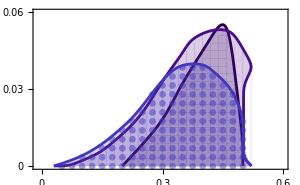

```mathematica
plot1=Show[horilinesfunc[ldev1P,{i,0,0.6,0.02},{j,0,0.06,0.003},{ColorData["DeepSeaColors",0],Thickness[0.0008],Opacity[pOp]},{ColorData["DeepSeaColors",0]}],
vertlinesfunc[ldev15P,{i,0,0.6,0.02},{j,0,0.06,0.003},{ColorData["DeepSeaColors",0.2],Thickness[0.001],Opacity[pOp]},{ColorData["DeepSeaColors",0.2]}],
dotsfunc[ldev2P,{i,0,0.6,0.025},{j,0,0.06,0.0035},{ColorData["DeepSeaColors",0.4],PointSize[0.016],Opacity[0.5]},{ColorData["DeepSeaColors",0.4]}]
]
```

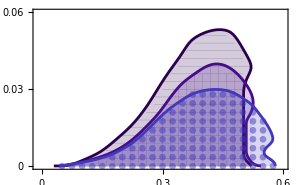

```mathematica
plot2=Show[horilinesfunc[yD0015P,{i,0,0.6,0.02},{j,0,0.06,0.003},{ColorData["DeepSeaColors",0],Thickness[0.001],Opacity[pOp]},{ColorData["DeepSeaColors",0]}],
vertlinesfunc[yD003P,{i,0,0.6,0.02},{j,0,0.06,0.003},{ColorData["DeepSeaColors",0.2],Thickness[0.001],Opacity[pOp]},{ColorData["DeepSeaColors",0.2]}],
dotsfunc[yD005P,{i,0,0.6,0.025},{j,0,0.06,0.0035},{ColorData["DeepSeaColors",0.4],PointSize[0.016],Opacity[0.5]},{ColorData["DeepSeaColors",0.4]}]
]
```

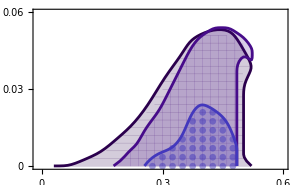

```mathematica
plot4=Show[horilinesfunc[zD0P,{i,0,0.6,0.02},{j,0,0.06,0.003},{ColorData["DeepSeaColors",0],Thickness[0.001],Opacity[pOp]},{ColorData["DeepSeaColors",0]}],
vertlinesfunc[zD01P,{i,0,0.6,0.02},{j,0,0.06,0.003},{ColorData["DeepSeaColors",0.2],Thickness[0.001],Opacity[pOp]},{ColorData["DeepSeaColors",0.2]}],
dotsfunc[zD02P,{i,0,0.6,0.025},{j,0,0.06,0.0035},{ColorData["DeepSeaColors",0.4],PointSize[0.016],Opacity[0.5]},{ColorData["DeepSeaColors",0.4]}]
]
```

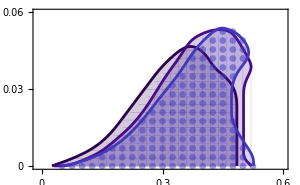

```mathematica
plot5=Show[horilinesfunc[z006P,{i,0,0.6,0.02},{j,0,0.06,0.003},{ColorData["DeepSeaColors",0],Thickness[0.001],Opacity[pOp]},{ColorData["DeepSeaColors",0]}],
vertlinesfunc[z001P,{i,0,0.6,0.02},{j,0,0.06,0.003},{ColorData["DeepSeaColors",0.2],Thickness[0.001],Opacity[pOp]},{ColorData["DeepSeaColors",0.2]}],
dotsfunc[z012P,{i,0,0.6,0.025},{j,0,0.06,0.0035},{ColorData["DeepSeaColors",0.4],PointSize[0.016],Opacity[0.5]},{ColorData["DeepSeaColors",0.4]}]
]
```

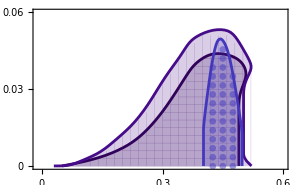

```mathematica
plot6=Show[horilinesfunc[dy002,{i,0,0.6,0.02},{j,0,0.06,0.003},{ColorData["DeepSeaColors",0],Thickness[0.001],Opacity[pOp]},{ColorData["DeepSeaColors",0]}],
vertlinesfunc[dy005,{i,0,0.6,0.02},{j,0,0.06,0.003},{ColorData["DeepSeaColors",0.2],Thickness[0.001],Opacity[pOp]},{ColorData["DeepSeaColors",0.2]}],
dotsfunc[dy008,{i,0,0.6,0.025},{j,0,0.06,0.0035},{ColorData["DeepSeaColors",0.4],PointSize[0.016],Opacity[0.5]},{ColorData["DeepSeaColors",0.4]}]
]
```

```mathematica
dummy=Graphics[ImageSize->{60,100}];
```

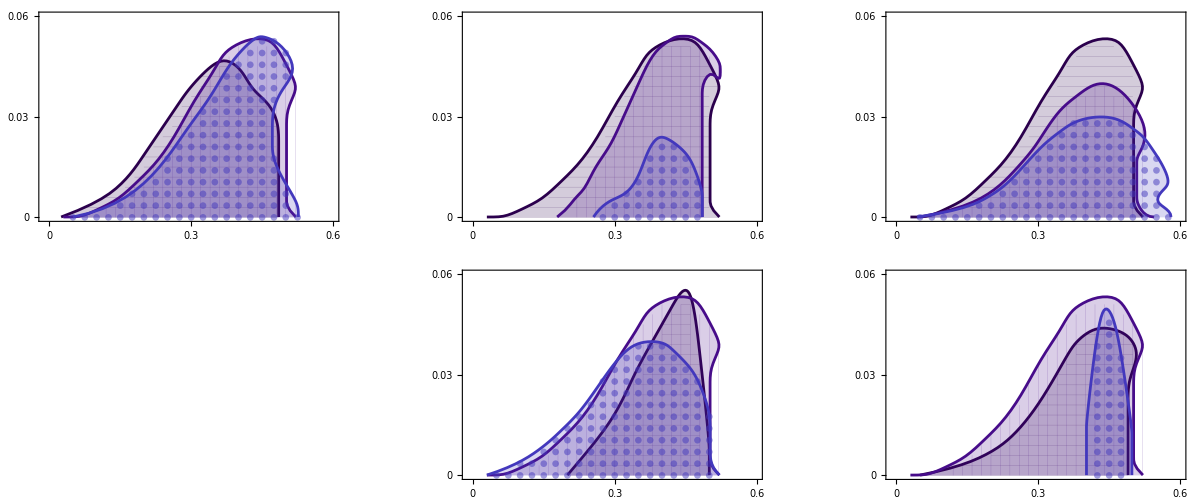

```mathematica
plot=Show[GraphicsGrid[{{plot5,dummy,plot4,dummy,plot2,dummy},{SpanFromLeft,dummy,plot1,dummy,plot6,dummy}},ImageSize->{1200,500},Spacings->{Scaled[0],Scaled[0.1]}],
Graphics[{Text[Style["a",20,FontFamily->"Latin Modern Math"],{14,15}],
Text[Style["b",20,FontFamily->"Latin Modern Math"],{380,15}],
Text[Style["c",20,FontFamily->"Latin Modern Math"],{740,15}],
Text[Style[Rotate["Inverse Froude Number, γ",Pi/2],24,FontFamily->"Latin Modern Roman 10"],{-25,-180}],
Text[Style["Frequency Ratio, φ",24,FontFamily->"Latin Modern Roman 10"],{530,-410}],


Text[Style["z_0",24,FontFamily->"Latin Modern Roman 10"],{305,-55}],
Text[Style["(ż)_0",24,FontFamily->"Latin Modern Roman 10"],{665,-55}],
Text[Style["(ẏ)_0",24,FontFamily->"Latin Modern Math"],{1025,-55}],
Text[Style["ℓ_d",24,FontFamily->"Latin Modern Roman 10"],{665,-255}],
Text[Style["δy",24,FontFamily->"Latin Modern Roman 10"],{1025,-255}]


}]
]
```

```mathematica
plotF=Overlay[{plot,
Graphics[Inset[Labeled[legendhori,"0.6",Right,LabelStyle->{Black,16,FontFamily->"Latin Modern Math"}],Scaled[{0.07,0.75}]],ImageSize->{1200,500}],
Graphics[Inset[Labeled[legendvert,"1",Right,LabelStyle->{Black,16,FontFamily->"Latin Modern Math"}],Scaled[{0.059,0.7}]],ImageSize->{1200,500}],
Graphics[Inset[Labeled[legendpoint,"1.2",Right,LabelStyle->{Black,16,FontFamily->"Latin Modern Math"}],Scaled[{0.077,0.65}]],ImageSize->{1200,500}],

Graphics[Inset[Labeled[legendhori,"0",Right,LabelStyle->{Black,16,FontFamily->"Latin Modern Math"}],Scaled[{0.85,0.75}]],ImageSize->{1200,500}],
Graphics[Inset[Labeled[legendvert,"-0.1",Right,LabelStyle->{Black,16,FontFamily->"Latin Modern Math"}],Scaled[{0.85,0.7}]],ImageSize->{1200,500}],
Graphics[Inset[Labeled[legendpoint,"-0.2",Right,LabelStyle->{Black,16,FontFamily->"Latin Modern Math"}],Scaled[{0.85,0.65}]],ImageSize->{1200,500}],

Graphics[Inset[Labeled[legendhori,"0.015",Right,LabelStyle->{Black,16,FontFamily->"Latin Modern Math"}],Scaled[{2.3,0.75}]],ImageSize->{1200,500}],
Graphics[Inset[Labeled[legendvert,"0.03",Right,LabelStyle->{Black,16,FontFamily->"Latin Modern Math"}],Scaled[{2.278,0.7}]],ImageSize->{1200,500}],
Graphics[Inset[Labeled[legendpoint,"0.05",Right,LabelStyle->{Black,16,FontFamily->"Latin Modern Math"}],Scaled[{2.28,0.65}]],ImageSize->{1200,500}],



Graphics[Inset[Labeled[legendhori,"1",Right,LabelStyle->{Black,16,FontFamily->"Latin Modern Math"}],Scaled[{0.828,0.32}]],ImageSize->{1200,500}],
Graphics[Inset[Labeled[legendvert,"1.5",Right,LabelStyle->{Black,16,FontFamily->"Latin Modern Math"}],Scaled[{0.839,0.27}]],ImageSize->{1200,500}],
Graphics[Inset[Labeled[legendpoint,"2",Right,LabelStyle->{Black,16,FontFamily->"Latin Modern Math"}],Scaled[{0.827,0.22}]],ImageSize->{1200,500}],


Graphics[Inset[Labeled[legendhori,"0.02",Right,LabelStyle->{Black,16,FontFamily->"Latin Modern Math"}],Scaled[{2.3,0.32}]],ImageSize->{1200,500}],
Graphics[Inset[Labeled[legendvert,"0.05",Right,LabelStyle->{Black,16,FontFamily->"Latin Modern Math"}],Scaled[{2.3,0.27}]],ImageSize->{1200,500}],
Graphics[Inset[Labeled[legendpoint,"0.08",Right,LabelStyle->{Black,16,FontFamily->"Latin Modern Math"}],Scaled[{2.28,0.22}]],ImageSize->{1200,500}]

}]
```

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
Export["C:\\Users\\by2475\\Dropbox\\NYU POSTDOC DRIVE\\Ants Project\\Mathematica\\2D model\\Updated Figures\\feasibleregion.pdf",plotF]
```

C:\Users\by2475\Dropbox\NYU POSTDOC DRIVE\Ants Project\Mathematica\2D model\Updated Figures\feasibleregion.pdf